```mathematica
Clear["Global`*"]
Q = {{1-α-β,α,β},{β,1-α-β,α},{α,β ,1-α-β}}; (*Circulant - Special Case of Double Stohastic*)
Q//MatrixForm
```

(1-α-β | α | β
β | 1-α-β | α
α | β | 1-α-β)

```mathematica
P = {{1,0,1+w},{1+w,1,0},{0,1+w,1}};
P//MatrixForm
```

(1 | 0 | 1+w
1+w | 1 | 0
0 | 1+w | 1)

```mathematica
Frequency = {x,y,z};
Fitness = P.Frequency;
ϕ = Frequency.Fitness //FullSimplify;
RHSX = x*Q[[1,1]]*Fitness[[1]] + y*Q[[2,1]]*Fitness[[2]] + z*Q[[3,1]]*Fitness[[3]]-x*ϕ;
RX = RHSX /. {z -> 1-x-y} //FullSimplify;
RHSY = x*Q[[1,2]]*Fitness[[1]] + y*Q[[2,2]]*Fitness[[2]] + z*Q[[3,2]]*Fitness[[3]]-y*ϕ;
RY = RHSY /. {z -> 1-x-y} //FullSimplify;
F = {RX,RY};
G = F/. {x -> u-(v/3^{1/2}),y -> 2*v/3^{1/2}};
xp = Part[G,1];
yp = Part[G,2];
vp = 3^{1/2}*yp/2;
up = xp + yp/2;
H = {up,vp}//FullSimplify;
F = H/. {u->x+1/2, v-> y+1/(2*3^{1/2})}// FullSimplify;
X = {x,y};
F = Flatten[F];
F/.{x->0,y->0};
```

```mathematica
(*Given an (α,β), want to find Hopf in w*)
```

```mathematica
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->0,y->0}//FullSimplify;
Jacc // MatrixForm
```

(1/6 (1-9 α-w (1+3 α)-6 β) | (-1-α+4 β+w (-1+α+2 β))/(2 √3)
(1+w+α-w α-2 (2+w) β)/(2 √3) | 1/6 (1-9 α-w (1+3 α)-6 β))

```mathematica
Eigenvalues[Jacc]//FullSimplify
```

{1/6 (1-9 α-w (1+3 α)-6 β-√3 √(-(1+w+α-w α-2 (2+w) β)^2)),1/6 (1-9 α-w (1+3 α)-6 β+√3 √(-(1+w+α-w α-2 (2+w) β)^2))}

```mathematica
traceFP[α_,w_] =Tr[Jacc]//FullSimplify;
determinantFP[α_,w_] =Det[Jacc]//FullSimplify;
```

```mathematica
Solve[1/3 (1-9 α-w (1+3 α)-6 β)==0,w]
```

{{w→(1-9 α-6 β)/(1+3 α)}}

```mathematica
Minimize[{(1-9 α-6 β)/(1+3 α),0<α<1/9,0<β<1/6 (1-9 α)},{α,β}];
```

```mathematica
Maximize[{(1-9 α-6 β)/(1+3 α),0<α<1/9,0<β<1/6 (1-9 α)},{α,β}];
```

```mathematica
1/9 (1+w+w^2-3 α+3 w α+21 α^2+12 w α^2+3 w^2 α^2+3 (-3-w (2+w)+7 α+w (4+w) α) β+3 (7+w (4+w)) β^2)/.{w->(1-9 α-6 β)/(1+3 α)}//FullSimplify(*determinant at trace=0*)
```

((1+6 α^2+6 (-1+β) β+α (-3+6 β))^2)/(3 (1+3 α)^2)

```mathematica
(*which is positive! so we have a Hopf at w=(1-9 α-6 β)/(1+3 α) so long as α<1/9 andβ<1/6(1-9α)*)
```

```mathematica
JaccHopf = Jacc /.{w->(1-9 α-6 β)/(1+3 α)}//FullSimplify;
JaccHopf //MatrixForm
```

(0 | (-1-6 α^2+α (3-6 β)-6 (-1+β) β)/(√3 (1+3 α))
(1+6 α^2+6 (-1+β) β+α (-3+6 β))/(√3 (1+3 α)) | 0)

```mathematica
ω = (1+6 α^2+6 (-1+β) β+α (-3+6 β))/(√3 (1+3 α));
f = XP +ω*y //FullSimplify;
g = YP -ω*x //FullSimplify;
anearly = ((D[f,{x,3}]+ D[f,{x,1},{y,2}]+ D[g,{x,2},{y,1}]+D[g,{y,3}]) + (1/ω)*(D[f,x,y]*(D[f,{x,2}]+D[f,{y,2}])-D[g,x,y]*(D[g,{x,2}]+D[g,{y,2}]) - D[f,{x,2}]*D[g,{x,2}]+D[f,{y,2}]*D[g,{y,2}]))/16 //FullSimplify;
a = anearly/.{x->0,y->0}//FullSimplify;
a
```

-1+w

```mathematica
(*So, given a circulant mutation matrix with α<1/9 andβ<1/6(1-9α), there is a supercritical hopf in RPS dynamics at w=(1-9 α-6 β)/(1+3 α), which allows for hopfs from w=0 to w=1 but not for w>1.

A better way of saying this may be just that β<1/6(1-9α), since if this holds and if α>1/9 then β<0.
*)
```

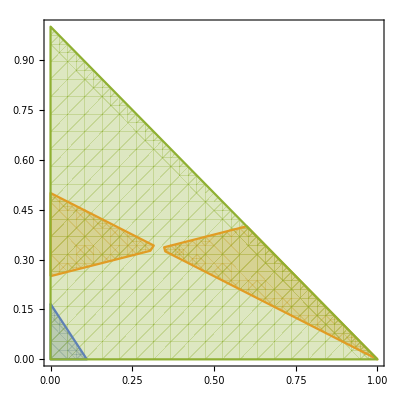

```mathematica
RegionPlot[{0<β<1/6(1-9α),(3 β≤1&&((α+2 β>1&&α+β≤1)||(α>0&&1+α<4 β)))||(3 β>1&&((α>0&&α+2 β<1)||(1+α>4 β&&α+β≤1))),α+β<=1},{α,0,1},{β,0,1}]
```

```mathematica
(*If α,β don't allow for zero trace then the trace is negative and the determinant is positive, so the fixed point will be a stable equilibrium.
In the orange shaded region above there is a single value of w =(1+α-4 β)/(-1+α+2 β) , at which the fixed has negative real roots.
*)
```

```mathematica
Solve[(traceFP[α,w])==-Sqrt[ 4*determinantFP[α,w]],w];
Reduce[{0<(1+α-4 β)/(-1+α+2 β),0<α<1,0<β<1,α+β<=1}]//FullSimplify;
```